## Gaussian Beam Propagation

Rainer Kaltenbaek, 14th-17th Sept. 2007

turning off annoying warnings:

```mathematica
Off[General::"spell1"]
```

```mathematica
Off[General::"spell"]
```

### definitions of Gaussian beam parameters

the following calculates the Rayleigh length depending on the wavelength and the waist of a beam:

```mathematica
zR[w0_,λ_]:=(Pi w0^2)/λ
```

calculate waist from Rayleigh length and wavelength:

```mathematica
w0[zR_,λ_]:=√((λ zR)/Pi)
```

calculate beam radius at position z from waist:

```mathematica
w[z_,w0_,λ_]:=w0 √(1+((z λ)/(Pi w0^2))^2)
```

```mathematica
wk[z_,zR_,k_]:=√(2/(k zR) (zR^2+z^2))
```

```mathematica
Simplify[Normal[Series[w[z,gw0,λ],{z,∞,0}]],Assumptions->{gw0>0,λ>0}]
```

(√(z^2) λ)/(gw0 π)

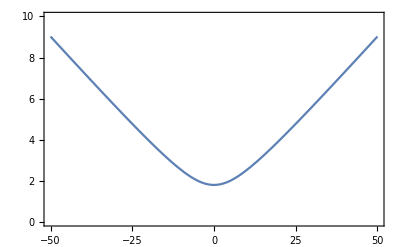

```mathematica
Plot[1.8*√(1+((z 1.)/(Pi 1.8^2))^2),{z,-50,50},PlotRange->{0,10},Frame->True,Axes->None]
```

```mathematica
w[q_,λ_]:=w0[Im[q],λ] √(1+(Re[q]/Im[q])^2)
```

the radius of curvature of the wavefronts is:

```mathematica
R[z_,z0_]:=z (1+(z0/z)^2)
```

let’s define that as a function of q:

```mathematica
R[q_]:=Re[q] (1+(Im[q]/Re[q])^2)
```

calculate the divergence angle of a beam with waist w0 and wavelength λ:

```mathematica
gθ[w0_,λ_]:=λ/(Pi w0)
```

M^2 factor:

```mathematica
M2factor[θ_,gw0_,λ_]:=θ/gθ[gw0,λ]
```

### using ABCD matrices to represent optical elements

given the complex beam parameter qOld before the optical element that is represented by the matrix A we can calculate the complex beam parameter qNew after the optical element with the following expression:

```mathematica
qNew[A_,qOld_]:=(A[[1,1]] qOld+A[[1,2]])/(A[[2,1]] qOld + A[[2,2]])
```

the matrix representing a lens of focal length f:

```mathematica
Mlens[f_]:={{1,0},{-1/f,1}}
```

reflection on a curved mirror with curvature radius R - R>0 for a concave mirror

```mathematica
Msphmirror[R_]:={{1,0},{-2/R,1}}
```

the following holds also for a thicker spherical mirror - as long as the paraxial approximation is still okay (t: thickness of the mirror substrate at the edge of the mirror, r: radius of the mirror substrate, Rs: radius of curvature of the mirror, n1: index of refraction outside the mirror substrate, n2: index of refraction of the mirror substrate) - TO BE PRECISE - this holds for a beam being transmitted through a spherical mirror coming from the curved side and passing out again via the flat side:

```mathematica
MsphmirrorExact[t_,r_,Rs_,n1_,n2_]:=Module[{d},
d=t-(Rs-√(-r^2+Rs^2));
{{1+(d (n1-n2))/(n2 Rs),(d n1)/n2},{(n1-n2)/(n1 Rs),1}}
]
```

this results from:

```mathematica
Simplify[Mref[n2,n1].Mfree[d].MCurveRef[n1,n2,Rs]]
```

{{1+(d (n1-n2))/(n2 Rs),(d n1)/n2},{(n1-n2)/(n1 Rs),1}}

the following is a matrix desribing a beam entering a spherical mirror via the flat side and being reflected from the curved side, passing through the medium again and leaving via the flat side once more:

```mathematica
MsphmirrorRef[t_,r_,Rs_,n1_,n2_]:=Module[{d},
d=t-(Rs-√(-r^2+Rs^2));{{1-(2 d)/Rs,-(2 d n1 (d-Rs))/(n2 Rs)},{-(2 n2)/(n1 Rs),1-(2 d)/Rs}}
]
```

which is derived from the following:

```mathematica
Simplify[{{1,0},{0,n2/n1}}.{{1,d},{0,1}}.{{1,0},{-2/Rs,1}}.{{1,d},{0,1}}.{{1,0},{0,n1/n2}},Assumptions->{n1>0,n2>0,d>0,Rs∈Reals}]
```

{{1-(2 d)/Rs,-(2 d n1 (d-Rs))/(n2 Rs)},{-(2 n2)/(n1 Rs),1-(2 d)/Rs}}

in other words :

```mathematica
Simplify[Mref[n2,n1].Mfree[d].Msphmirror[Rs].Mfree[d].Mref[n1,n2]]
```

{{1-(2 d)/Rs,-(2 d n1 (d-Rs))/(n2 Rs)},{-(2 n2)/(n1 Rs),1-(2 d)/Rs}}

the matrix representing free-space propagation:

```mathematica
Mfree[L_]:={{1,L},{0,1}}
```

ray transfer matrix for the refraction of a beam going from a medium with refractive index n1 to a medium with refractive index n2 - the interface is flat:

```mathematica
Mref[n1_,n2_]:={{1,0},{0,n1/n2}}
```

same thing but with a curved surface, where R is the radius of curvature (R>0 for a convex surface, i.e.m the center of the curvature is after the interface):

```mathematica
MCurveRef[n1_,n2_,R_]:={{1,0},{(n1-n2)/(R n2),n1/n2}}
```

the following gives the transfer matrix for a beam passing through a flat piece of material of thickness d. The index of refraction of the material is n2 - the index of refraction outside of the material is n1:

```mathematica
Mtrans[n1_,n2_,d_]:=Mref[n2,n1].Mfree[d].Mref[n1,n2]
```

The following takes a complex beam parameter qOld. It is supposed to be the parameter of a Gaussian beam at some reference position. The second parameter is an array O. Each of its elements is of the form {x,M}, where M is the matrix of some optical element (e.g. a lens) and x is the distance of that element from the reference position, for which qOld is defined. Suppose O={{x1,M1},{x2,M2},{x3,M3}} and that x2>x1>x3. The function will automatically put the matrices M1 to M3 in the correct order: M2 x M1 x M3 and apply the matrices for free-space propagation in between, so the result of the function will be

qNew[M3,
qNew[Mfree[x2-x1],
qNew[M1,
qNew[Mfree[x1-x3],
qNew[M3,
qNew[Mfree[x3],
qOld]]]]]]

```mathematica
optics[qOld_,OptEl___]:=Module[{zO,OE,rf,qTemp,i,altPos},
(*get OptEl into array form: *)
OE={OptEl};
(*determine the length of the array*)
zO=Length[OE];
(*get the correct "reihenfolge" (ordering) of the optical elements in O depending on their distance from the reference position*)
rf=Ordering[OE[[All,1]]];
(*sort OE accordingly*)
OE=OE[[rf]];
(*set temporary q to start value*)
qTemp=qOld;
(*set current position*)
altPos=0;
For[i=1,i≤zO,i++,
(*perform free propagation between optical elements*)
qTemp=qNew[Mfree[OE[[i,1]]-altPos],qTemp];
altPos=OE[[i,1]];
(*apply the matrix for the optical element itself*)
qTemp=qNew[OE[[i,2]],qTemp];
];
qTemp
]
```

example for the use of the "optics" function: a beam is passed (1) through a lense that is closer than its focal length (green line) and (2) through a lense that is further away than its focal length (red line)

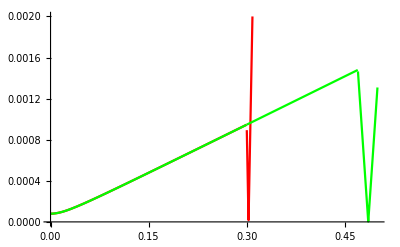

```mathematica
Module[{q1,q2,z1,z2,x1,x2,qOld},
x1=0.30;
x2=0.47;
qOld=I zR[80 10^-6,7.9 10^-7];
q1=optics[qOld,{x1,Mlens[0.0028]}];
q2=optics[qOld,{x2,Mlens[0.0154]}];
Plot[{w[
UnitStep[z-x1] qNew[
Mfree[z-x1],
q1
]+UnitStep[x1-z] qNew[Mfree[z],qOld],7.9 10^-7],w[
UnitStep[z-x2] qNew[
Mfree[z-x2],
q2
]+UnitStep[x2-z] qNew[Mfree[z],qOld],7.9 10^-7]},{z,0,0.5},PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0]},PlotRange->{0,0.002}]
]
```

### characterizing the single-mode fibers

1/e width of a gaussian mode in a step-index fiber with core diameter d (Marcuse’s equation: D. Marcuse, “Loss analysis of single-mode fiber splices”, Bell Syst. Tech. J. 56, 703 (1977)):

```mathematica
fiberWidth[d_,V_]:=d (0.65+1.619/V^1.5+2.879/V^6)
```

the "V-number" is the normalized frequency parameter of the fiber (a is the fiber core radius):

```mathematica
Vnumber[NA_,a_,λ_]:=2 Pi NA a/λ
```

the core radius of the fiber as a function of V, λ and NA:

```mathematica
coreradius[NA_,V_,λ_]:=V λ/(2 Pi NA)
```

saving the functions I have defined in this notebook so far:

```mathematica
Save["/home/rainer/physik/programme/Mathematica/Gauss/gaussdefs", {zR,w0,w,R,gθ,qNew,Mlens,Msphmirror,Mfree,Mref,MCurveRef,Mtrans,optics,fiberWidth,Vnumber,coreradius}]
```

the core radius of our fibers is:

```mathematica
fcore=coreradius[0.12,2,790 10^-9]
```

2.09554×10^-6

```mathematica
fcore=coreradius[0.12,2,790 10^-9]
```

2.09554×10^-6

the wavelength in our experiments is (in nm):

```mathematica
expλ=790 10^-9;
```

now we compare that to the mode-field diameter (5.6 μm) that Thorlabs gives for their P1-830A-FC-5 (and related) fibers (measured at 830nm) - if we assume a V-number of 2, we see that the calculated value fits well with the value given by Thorlabs:

```mathematica
fiberWidth[2 coreradius[0.12,2,790 10^-9],2]
```

5.31172×10^-6

that means for our wavelength (810nm) we have a mode-field radius of:

```mathematica
fwaist=fiberWidth[2 fcore,Vnumber[0.12,fcore,expλ]]/2
```

2.65586×10^-6

trying to calculate the mode-field waist of a 1064nm single-mode fiber (in mm):

```mathematica
optics[I zR[0.7,1064. 10^-6],{8.13,Mlens[8.13]}]
```

-8.13+0.0456853 ⅈ

```mathematica
w0[0.04568533001210591,1064. 10^-6]
```

0.00393355

on the Thorlabs home page they said 3.1 mm for the fiber we have - so we seem to have been a bit off with our measurement of the 0.7mm waist of the collimated beam.

### match fiber waist to UV-pump waist

say the UV waist is (in m)

```mathematica
UVwaist=130 10^-6;
```

how do we get the optimal distance of the coupler's lens to the crystal? we start with a beam of Rayleigh length z0, go over a distance Dist, then apply a lens of focallength bw -> the beam parameter we get is:

```mathematica
qNew[Mlens[bw],Dist+I z0]
```

(Dist+ⅈ z0)/(1-(Dist+ⅈ z0)/bw)

if we complex expand that we get:

```mathematica
ComplexExpand[(Dist+ⅈ z0)/(1-(Dist+ⅈ z0)/bw)]
```

Dist/((1-Dist/bw)^2+z0^2/bw^2)-Dist^2/(bw ((1-Dist/bw)^2+z0^2/bw^2))+(ⅈ z0)/((1-Dist/bw)^2+z0^2/bw^2)-z0^2/(bw ((1-Dist/bw)^2+z0^2/bw^2))

The complex part of that is the rayleighlength of the new beam:

```mathematica
FullSimplify[z0/((1-Dist/bw)^2+z0^2/bw^2)]
```

(bw^2 z0)/((bw-Dist)^2+z0^2)

That has to be equal to the Rayleigh length zL a beam has in the fiber:

```mathematica
Solve[zL==(bw^2 z0)/((bw-Dist)^2+z0^2),Dist]
```

{{Dist→(bw zL-√(bw^2 z0 zL-z0^2 zL^2))/zL},{Dist→(bw zL+√(bw^2 z0 zL-z0^2 zL^2))/zL}}

The Distance of the lens to the crystal should definitely be larger than the focal length of our lens - therefore the second solution must be correct:

```mathematica
optimalDistance[f_]:=Module[{zL,z0},
zL=zR[fwaist,expλ];
z0=zR[UVwaist,expλ];
(f zL+√(f^2 z0 zL-z0^2 zL^2))/zL
]
```

```mathematica
optimalDistance[0.011]
```

0.545221

given a lens with focal length f, what is the distance of the lens to the UV waist necessary to map the UV waist to the fiber mode?

```mathematica
optDistance[f_]:=Module[{w0,λ,wf},
w0=UVwaist;
λ=expλ;
wf=fwaist;
f+(√(-π^2 w0^4 wf^4 λ^2+f^2 w0^2 wf^2 λ^4))/(wf^2 λ^2)
]
```

```mathematica
optDistance[15.4 10^-3]
```

0.766203

```mathematica
optDistance[11 10^-3]
```

0.545221

now we will draw the optimal distance of a lens matching the UV-pump waist to the fiber waist over the focal length of the lens:

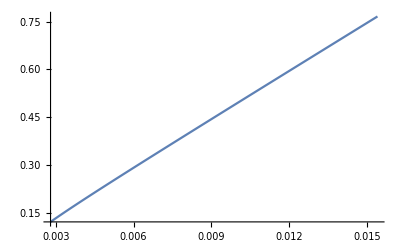

```mathematica
Plot[optDistance[f],{f,0.0028,0.0154}]
```

### Fiber Collimation Packages

the Thorlabs collimation package F220FC-B has a lens with a focal length of 11mm and it is adjusted for collimation with a SM600 fiber at a wavelength of 633nm -> we want to find out how it will perform at our wavelengths and with our fibers.

assuming a V-number of 2 for the SM600 fiber we get the following mode-field waist, which is in acceptably good accordance with the value given by Thorlabs:

```mathematica
SM600w=fiberWidth[2 coreradius[0.12,2,633 10^-9],2]/2
```

2.12805×10^-6

checking how far the collimation lens (11mm) in the Thorlabs collimation package F220FC-B has to be away from the fiber in order to optimally collimate the beam:

```mathematica
optColPos=Module[{x},NMinimize[Re[optics[I zR[SM600w,633 10^-9],{x,Mlens[0.011]}]],{x}][[2,1,2]]]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

0.0110225

plotting the collimated beams with our fibers and our wavelengths (red curve) compared to 633nm beam with SM600 fiber:

-0.015+8.22445 ⅈ

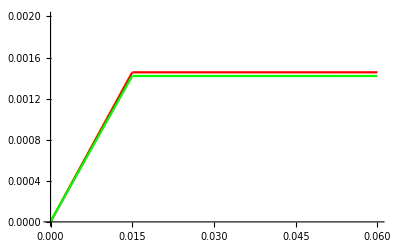

```mathematica
Module[{q1,q2,z1,z2,x,z,qOld1,qOld2,λ1,λ2},
x=0.015;
λ1=810 10^-9;
λ2=633 10^-9;
qOld2=I zR[SM600w,λ2];
qOld1=I zR[fwaist,λ1];
q1=optics[qOld1,{x,Mlens[0.015]}];
Print[q1];
q2=optics[qOld2,{x,Mlens[0.015]}];
Plot[{w[
UnitStep[z-x] qNew[
Mfree[z-x],
q1
]+UnitStep[x-z] qNew[Mfree[z],qOld1],λ1],w[
UnitStep[z-x] qNew[
Mfree[z-x],
q2
]+UnitStep[x-z] qNew[Mfree[z],qOld2],λ2]},{z,0,0.06},PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0]},PlotRange->{0,0.002}]
]
```

0.+0.198521 ⅈ

-0.1+0.0644578 ⅈ

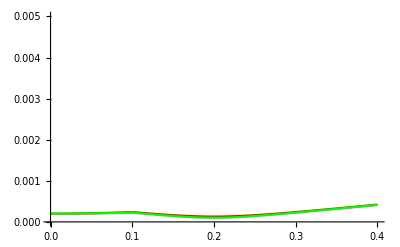

```mathematica
Module[{q1,q2,z1,z2,x,z,qOld1,qOld2,λ1,λ2},
x=0.1;
λ1=810 10^-9;
λ2=633 10^-9;
qOld2=I zR[0.0002,λ2];
qOld1=I zR[0.0002,λ1];
q1=optics[qOld1,{x,Mlens[0.1]}];
Print[qOld2];
Print[q1];
q2=optics[qOld2,{x,Mlens[0.1]}];
Plot[{w[
UnitStep[z-x] qNew[
Mfree[z-x],
q1
]+UnitStep[x-z] qNew[Mfree[z],qOld1],λ1],w[
UnitStep[z-x] qNew[
Mfree[z-x],
q2
]+UnitStep[x-z] qNew[Mfree[z],qOld2],λ2]},{z,0,0.4},PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0]},PlotRange->{0,0.005}]
]
```

assume we have a UV beam emerging from a 25 μm pinhole (that's the diameter) - how do we have to focus it to get a waist of 100 μm diameter at the correct distance (somewhere between 20 and 60 cm)?

```mathematica
Module[{f,qN},
f=0.1;
qN=optics[I zR[12.5 10^-6,405 10^-9],{5 f/4,Mlens[f]}];
Print[w0[Im[qN],405 10^-9]];
Print[-Re[qN]];]
```

0.0000499413

0.499062

assume we have a UV beam emerging from a 50 μm pinhole (that's the diameter) - how do we have to focus it to get a waist of 100 μm diameter at the correct distance (somewhere between 20 and 60 cm)?

```mathematica
Module[{f,qN},
f=0.1;
qN=optics[I zR[25 10^-6,405 10^-9],{5 f/4,Mlens[f]}];
Print[w0[Im[qN],405 10^-9]];
Print[-Re[qN]];
]
```

0.0000981711

0.485502